## RK Stuff

```mathematica
BSTable=Association[{
"A"->({{0, 0, 0, 0}, {1/2, 0, 0, 0}, {0, 3/4, 0, 0}, {2/9, 1/3, 4/9, 0}}),
"bH"->{2/9,1/3,4/9,0},"orderH"->3,
"bL"->{7/24,1/4,1/3,1/8},"orderL"->2,
"c"->{0,1/2,3/4,1}
}];
DorPrinceTable=Association[{
"A"->({{0, 0, 0, 0, 0, 0}, {1/5, 0, 0, 0, 0, 0}, {3/40, 9/40, 0, 0, 0, 0}, {44/45, -56/15, 32/9, 0, 0, 0}, {19372/6561, -25360/2187, 64448/6561, -212/729, 0, 0}, {9017/3168, -355/33, 46732/5247, 49/176, -5103/18656, 0}, {35/384, 0, 500/1113, 125/192, -2187/6784, 11/84}}),
"bH"->{35/384, 0, 500/1113, 125/192,-2187/6784, 11/84,0},"orderH"->5,
"bL"->{5179/57600, 0, 7571/16695, 393/640,−92097/339200,187/2100, 1/40},
"orderL"->4,
"c"->{0, 1/5, 3/10, 4/5,8/9,1, 1}
}];
```

```mathematica
RKStep[f_,BT_][{h_,t0_,y0_}]:= Module[
{A,bH,bL,c,p,s,z,K},
(* Extract Data from Association *)
{A,bH,bL,c,p}=Map[BT,{"A","bH","bL","c","orderL"}];
s=Length[A];
(* Assign space for and compute internal slopes *)
K=ConstantArray[0.0,{Length[y0],s}];
Do[
z=y0+h*Sum[A⟦i,j⟧ K⟦All,j⟧,{j,1,i-1}];
K⟦All,i⟧=f[t0+c⟦i⟧h,z],
{i,1,s}]; 
(* Compute and return potential updated t, yH, and yL *)
{t0+h, 
y0+h*Sum[bH⟦i⟧K⟦All,i⟧,{i,1,s}], (*High Order*)
y0+h*Sum[bL⟦i⟧K⟦All,i⟧,{i,1,s}]}
]
```

## Making a Stiff ODE

```mathematica
Q=Orthogonalize[ RandomReal[{-1,1},{3,3}]];
Mat= Q.{
{-1000, 0, 0},
{0, -0.5, 3},
{0, -3, -0.5}
}.Qᵀ;
MatrixForm[Mat]
Chop[Eigensystem[Mat]]//TableForm
```

(-1.31737 | -12.6371 | -25.7991
-7.00499 | -118.503 | -322.456
-27.8607 | -322.285 | -881.18)

-1000. | -0.5+3. ⅈ | -0.5-3. ⅈ
-0.0285969
-0.343602
-0.93868 | 0.706818
-0.00695083-0.664019 ⅈ
-0.0189889+0.243062 ⅈ | 0.706818
-0.00695083+0.664019 ⅈ
-0.0189889-0.243062 ⅈ

## Stiff ODE Behavior

We made a matrix with some targeted eigenvalues.  The system has very different time frames,

```mathematica
f[y_]:= ({{-1.317373755856907, -12.637066224961245, -25.799111734793}, {-7.00498608217856, -118.5029992619306, -322.45644285578237}, {-27.86072107944938, -322.2848614602335, -881.1796269822127}}).y
{{λ1,λ2,λ3},{v1,v2,v3}}=Chop[Eigensystem[({{-1.317373755856907, -12.637066224961245, -25.799111734793}, {-7.00498608217856, -118.5029992619306, -322.45644285578237}, {-27.86072107944938, -322.2848614602335, -881.1796269822127}})]];
y0=RandomReal[{-2,2},3];
TMax=4.5;
ySol=NDSolveValue[{y'[t]==f[y[t]], y[0]==y0},y,{t, 0 ,TMax}];
Show[
ParametricPlot3D[ySol[t],{t, 0, TMax},PlotRange->All],
Graphics3D[{Arrow[{v1,{0,0,0}}],Arrow[{-v1,{0,0,0}}]}]
]
```

-Graphics3D-

The big negative eigenvalue gives explicit solver conniptions.  It is easy to explain what it does when we know the eigenvalues.

## Stability

Suppose we have the scalar IVP ODE y'=λ y with y(0)=y_0 which has solution y=y_0 ⅇ^(λ t).  We want to see how well our ODE solver works on this simple problem.   The problem is so simple that we can do this analytically. We get two polynomials!

```mathematica
Clear[f,t,y,y0,λ,h]
f[t_,y_]:=λ y
RKStep[f,BSTable][{h,0,{y0}}]//Simplify
RKStep[f,DorPrinceTable][{h,0,{y0}}]/.{y0->1, λ->z/h}//Simplify
```

{h,{1/6 y0 (6+6 h λ+3 h^2 λ^2+h^3 λ^3)},{1/48 y0 (48+48 h λ+24 h^2 λ^2+9 h^3 λ^3+h^4 λ^4)}}

{h,{1/600 (600+600 z+300 z^2+100 z^3+25 z^4+5 z^5+z^6)},{1+z+z^2/2+z^3/6+z^4/24+(1097 z^5)/120000+(161 z^6)/120000+z^7/24000}}

Every explicit RK scheme applied to the linear test problem y'=λ y  gives 
	y_(n+1)=p(z)y_n
for a polynomial p evaluated at z=λ h.

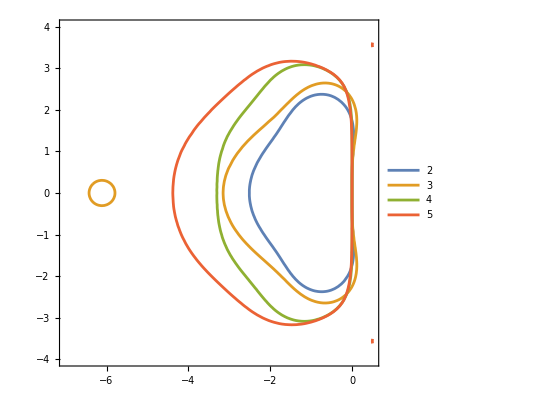

```mathematica
Clear[stabBS2,stabBS3]
stabBS2[z_]:=1/6 (6+6 z+3 z^2+z^3)
stabBS3[z_]:=1/48  (48+48 z+24 z^2+9 z^3+z^4)
stabDP4[z_]:=1/600 (600+600 z+300 z^2+100 z^3+25 z^4+5 z^5+z^6)
stabDP5[z_]:=1+z+z^2/2+z^3/6+z^4/24+(1097 z^5)/120000+(161 z^6)/120000+z^7/24000
ContourPlot[ {
Abs[stabBS2[x+I y]]==1,
Abs[stabBS3[x+I y]]==1,
Abs[stabDP4[x+I y]]==1,
Abs[stabDP5[x+I y]]==1},{x,-7,0.5},{y,-4,4},
PlotLegends->{"2","3","4","5"}]
```

The sad thing is that all explicit RK schemes have limited stability regions!

## Implicit Schemes

We worked out the simple Explicit Euler scheme
	y_(n+1)=y_n+h f(t_n,y_n)
by using the slope at the start of the step.   The very similar looking Implicit Euler formula
	y_(n+1)=y_n+h f(t_(n+1),y_(n+1))
 uses the slope at the end of the step. For our linear test problem y'=f(y)=λ y we can rearrange
 	y_(n+1)=y_n+h f(t_(n+1),y_(n+1))=y_n+λ h y_(n+1)
 and solve to find that
 	y_(n+1)=1/(1 - λ h)y_n.
 The stability function for the Implicit Euler scheme is 1/(1- z)

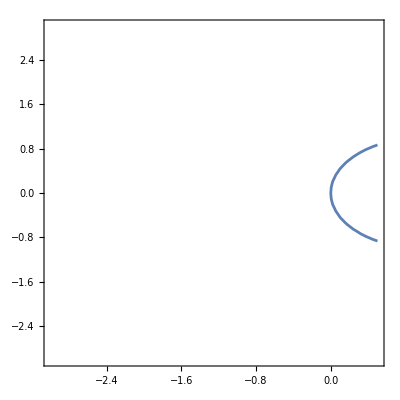

```mathematica
stabImpEuler[z_]:=1/(1-z)
ContourPlot[ Abs[stabImpEuler[x+I y]]==1,{x,-3,0.5},{y,-3,3}]
```

The stability functions of implicit RK schemes are rational functions.

## Approximations to ⅇ^(λ h)

Since the solution of y'=λ y with y(0)=1 is y(t)=ⅇ^(λ t) our schemes must approximate ⅇ^(λ h)=ⅇ^z.

```mathematica
Series[E^z,{z,0,7}]
Series[1/(1-z),{z,0,2}];
Series[1+z,{z,0,2}];
Series[stabBS2[z],{z,0,7}]
Series[stabBS3[z],{z,0,7}]
Series[stabDP4[z],{z,0,7}]
Series[stabDP5[z],{z,0,7}]
```

1+z+z^2/2+z^3/6+z^4/24+z^5/120+z^6/720+z^7/5040+O[z]^8

1+z+z^2/2+z^3/6+O[z]^8

1+z+z^2/2+(3 z^3)/16+z^4/48+O[z]^8

1+z+z^2/2+z^3/6+z^4/24+z^5/120+z^6/600+O[z]^8

1+z+z^2/2+z^3/6+z^4/24+(1097 z^5)/120000+(161 z^6)/120000+z^7/24000+O[z]^8

## Implementing Implicit Euler

At each step we need to solve
	y_(n+1)=y_n+h f(t_(n+1),y_(n+1))
for y_(n+1). This was easy enough when we had a scalar test problem f(t,y)=λ y.  It is still easy enough to write down if we have a linear vector system
	f(t,y)=A.y.
because we get
	y_(n+1)=y_n+h A y_(n+1)
which we can rearrange to get
	(I-h A)y_(n+1)=y_n
or equivalently
	y_(n+1)=(I -h A)^-1 y_n.
There is no solution formula for general  functions. This internal solve needs to be implemented iteratively.
For example using Newton’s Method. Starting with z_0=y_n and iterate
	z_(k+1)=z_k-(D_y f(t_n,z_k))^-1 f(t_n,z_k)
until converged. Define y_(n+1)=z_∞.

Implicit RK schemes are MUCH more complicated than explicit ones. Most practical ones make choices to keep the complexity under control.